Select the parameter (.prm) file of the desired chromatogram. It is assumed that the chromatography files are in the same directory as the parameter file.

```mathematica
SystemDialogInput["FileOpen" , {"C:/Users/fskdm/Dropbox", {"Parameter Files"->{"*.prm"}}}]
```

```mathematica
pfile ="C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_20_PhD_Last_Project\\2019_12_23_PAH_FAMEs\\Chromatograms\\RawData\\2020_02_06-172430.dat.prm"
```

C:\Users\fskdm\My PhD\Projects\2019_12_20_PhD_Last_Project\2019_12_23_PAH_FAMEs\Chromatograms\RawData\2020_02_06-172430.dat.prm

```mathematica
(*Extract the data directory:*)
filedir = FileNameJoin[ FileNameSplit[pfile][[1;;-2]]];

(*Import the parameters:*)
params = Import[pfile, "Lines"];

(*Create the data filename*)
file= FileNameJoin[
		{filedir
	,	FileNameSplit[
		StringSplit[                         
			params[[15]]                    (* Line 15 of the paramaters file contains the name of the data file *)
		][[3]]]                                        (* It is the third part of the line as separated by whitespace *)
		[[-1]]                                                 (* Select the last item on the list of the stringsplit *)
		}
	];(* Extract the filename *)
(* Show the result *)
Framed[TabView[{"Data"-> TableForm[{filedir, file}], "Parameters" -> params}]]
```

12

```mathematica
FrontEndTokenExecute["SaveRename", {StringJoin[file,".nb"]}]
```

```mathematica
data=BinaryReadList[file, {"Integer8"}~Join~Table["Real64", {17}], ByteOrdering->-$ByteOrdering];
```

```mathematica
Length[data[[1]]]
```

18

```mathematica
data[[-5;;-1]]//TableForm
```

2 | 12.931 | 306.106 | 294.268 | 5.28249 | 5.72791 | 2.03636×10^7 | 82870.8 | 660.186 | 649.447 | 0.0103882 | 626.874 | -0.0566345 | 2.0265×10^7 | 2.76769×10^7 | 693.15 | 673.15 | 623.15
2 | 12.955 | 306.105 | 294.259 | 5.26841 | 5.71554 | 2.03628×10^7 | 81231.9 | 660.196 | 649.429 | 0.0101501 | 627.419 | -0.0566284 | 2.0265×10^7 | 2.76769×10^7 | 693.15 | 673.15 | 623.15
2 | 12.978 | 306.106 | 294.254 | 5.26726 | 5.71458 | 2.03643×10^7 | 82808.9 | 660.199 | 649.298 | 0.0104034 | 627.472 | -0.0567139 | 2.0265×10^7 | 2.76769×10^7 | 693.15 | 673.15 | 623.15
3 | 901. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4 | 901. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
data[[1;;5]]//TableForm
```

0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 599.9 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2 | 0.034 | 303.69 | 293.749 | 2.33341 | 1.23684 | 2.02561×10^7 | 267691. | 581.145 | 635.463 | 0.0221527 | 222.934 | -0.0441803 | 2.0265×10^7 | 2.76769×10^7 | 683.15 | 673.15 | 253.15
2 | 0.056 | 303.692 | 293.736 | 0.741046 | 0.408344 | 2.02462×10^7 | 257920. | 581.084 | 635.704 | 0.0210907 | 222.934 | -0.0441864 | 2.0265×10^7 | 2.76769×10^7 | 683.15 | 673.15 | 253.15
2 | 0.078 | 303.692 | 293.773 | 0.553284 | 0.338474 | 2.02473×10^7 | 256312. | 581.113 | 635.61 | 0.0212433 | 233.532 | -0.04375 | 2.0265×10^7 | 2.76769×10^7 | 683.15 | 673.15 | 253.15

Plot the manifold temperatures:

```mathematica
ListPlot[{data[[All,9]]-273.12, data[[All, 10]]- 273.12,data[[All, 16]]- 273.12,data[[All,17]]- 273.12}
, PlotRange->{320, 400}
(*, PlotLegends->{"Inlet","Detector","Setpoint I","Setpoint D"} *)
, PlotLegends->SwatchLegend[{"Inlet","Detector","Setpoint I","Setpoint D"} ,LegendLabel->"Legend",LegendFunction->(Framed[#,Background->LightBlue]&)]
, AxesLabel->{"Sample","Manfold Temperature (°C)"}
, ImageSize->Large
,PlotLabel->"Reported Manifold temperatures"

]
```

-Graphics-

Just plot the temperatures:

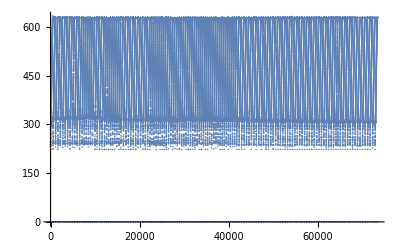

```mathematica
ListPlot[data[[All,12]]]
```

```mathematica
values={"ID", "Time", "TAmbient", "Ttc", "Vb", "dV", "P1", "P2", "TInlet", "TOutlet", "Detector", "TColumn", "Vcol","P1 Setpoint", "P2 Setpoint", "TInlet Setpoint", "TOutlet Setpoint", "TColumn Setpoint"}
```

{ID,Time,TAmbient,Ttc,Vb,dV,P1,P2,TInlet,TOutlet,Detector,TColumn,Vcol,P1 Setpoint,P2 Setpoint,TInlet Setpoint,TOutlet Setpoint,TColumn Setpoint}

```mathematica
Join[{values}, {Range[18] } ]//TableForm
```

ID | Time | TAmbient | Ttc | Vb | dV | P1 | P2 | TInlet | TOutlet | Detector | TColumn | Vcol | P1 Setpoint | P2 Setpoint | TInlet Setpoint | TOutlet Setpoint | TColumn Setpoint
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18

Split the data by ID. Turns the list into a list of lists.

```mathematica
data2 = Split[data, #1[[1]]==#2[[1]]&];
```

```mathematica
Length[data]
```

73301

```mathematica
Length[data2]
```

428

Find the times of the GC runs. This counts the number of GC runs, i.e. the length of the first dimension.

```mathematica
d1 = Select[data, #[[1]]==1&][[All, 2]];
```

```mathematica
d1
```

{539.9,542.,544.,546.,548.,549.9,551.9,553.9,555.9,557.9,559.9,561.9,563.9,565.9,567.9,569.9,571.9,573.9,575.9,577.9,579.8,581.9,583.9,585.9,588.,590.,591.8,593.8,595.8,597.8,599.8,601.8,603.8,605.8,607.8,609.8,611.8,613.8,615.8,617.8,619.9,621.9,623.9,625.9,627.9,629.9,631.9,633.9,635.9,637.9,639.9,641.9,643.9,645.9,647.9,649.9,651.9,653.8,655.8,657.8,659.8,661.8,663.9,665.9,667.9,669.9,671.9,673.7,675.7,677.7,679.7,681.7,683.7,685.7,687.7,689.7,691.7,693.7,695.7,697.7,699.7,701.8,703.8,705.8,707.8,709.8,711.8,713.8,715.9,717.9,719.9,721.9,723.9,725.9,727.9,729.9,731.9,733.9,735.9,737.9,739.9,741.9,743.9,745.9,747.9,749.9,752.,754.,756.,758.,760.,762.,764.,766.,768.,770.,772.1,774.1,776.1,778.1,779.8,781.8,783.8,785.8,787.8,789.8,791.8,793.7,795.7,797.7,799.7,801.7,803.7,805.7,807.8,809.8,811.8,813.8,815.8,817.7,819.7,821.7,823.7,825.7,827.7,829.7,831.7,833.6,835.5,837.5,839.6}

The number of GC runs:

```mathematica
Length[d1]
```

142

Check data integrity:
Number of GC runs (ID=2) + 2 per GC run (ID=1 and ID = 3) + ID=0 and ID=4

```mathematica
Length[d1]+Length[d1]*2 + 2
```

428

Plot a GC run to see if looks sane:

```mathematica
Manipulate[
ListLinePlot[
	Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
	, PlotLabel ->values[[dataset]]
]
	,{{gcrun,1,"GC Run"},1, Length[d1],1}
	,{{dataset,11, "Dataset"},1,18,1}
]
```

```mathematica
.
```

Delete wrong data:

First identify index of wrong data

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[107]][[All,2]]
```

{0.033,0.056,0.079,0.114,0.137,0.159,0.182,0.207,0.23,0.252,0.274,0.297,0.319,0.341,0.365,0.387,0.409,0.448,0.471,0.494,0.516,0.538,0.561,0.583,0.622,0.645,0.667,0.69,0.714,0.737,0.759,0.782,0.821,0.845,0.867,0.889,0.923,0.946,0.968,0.991,1.032,1.054,1.078,1.118,1.141,1.163,1.186,1.215,1.238,1.261,1.283,1.317,1.34,1.363,1.385,1.407,1.441,1.463,1.485,1.525,1.548,1.571,1.593,1.616,1.638,1.661,1.683,1.705,1.745,1.767,1.789,1.819,1.842,1.864,1.888,1.91,1.932,1.955,1.977,1.999,2.025,2.047,2.069,2.091,2.113,2.136,2.158,2.18,2.202,2.242,2.265,2.287,2.309,2.332,2.355,2.377,2.399,2.422,2.444,2.466,2.488,2.511,2.534,2.557,2.579,2.619,2.641,2.664,2.686,2.718,2.74,2.763,2.785,2.809,2.831,2.854,2.875,2.898,2.92,2.942,2.964,2.987,3.009,3.032,3.055,3.078,3.119,3.142,3.165,3.187,3.215,3.24,3.263,3.285,3.323,3.349,3.371,3.393,3.432,3.455,3.478,3.5,3.534,3.556,3.578,3.618,3.64,3.663,3.686,3.711,3.734,3.757,3.779,3.817,3.84,3.863,3.885,3.913,3.936,3.958,3.981,4.017,4.04,4.063,4.085,4.117,4.14,4.162,4.184,4.21,4.234,4.257,4.279,4.301,4.341,4.364,4.386,4.411,4.439,4.461,4.483,4.515,4.538,4.56,4.583,4.613,4.636,4.658,4.68,4.712,4.734,4.757,4.779,4.813,4.836,4.86,4.882,4.911,4.933,4.955,4.978,5.,5.035,5.058,5.08,5.106,5.128,5.152,5.174,5.197,5.219,5.241,5.264,5.286,5.311,5.335,5.359,5.381,5.403,5.44,5.464,5.486,5.514,5.537,5.561,5.583,5.609,5.632,5.655,5.677,5.699,5.722,5.746,5.768,5.79,5.82,5.845,5.868,5.89,5.914,5.937,5.961,5.983,6.01,6.032,6.054,6.077,6.099,6.122,6.145,6.167,6.189,6.211,6.233,6.256,6.278,6.313,6.337,6.36,6.382,6.419,6.441,6.465,6.487,6.51,6.533,6.556,6.578,6.611,6.633,6.655,6.677,6.7,6.722,6.744,6.767,6.79,6.814,6.838,6.86,6.883,6.907,6.93,6.954,6.977,6.999,7.021,7.045,7.07,7.093,7.115,7.139,7.162,7.184,7.209,7.231,7.253,7.276,7.298,7.32,7.343,7.366,7.388,7.411,7.433,7.457,7.479,7.513,7.536,7.56,7.582,7.608,7.632,7.655,7.677,7.699,7.721,7.745,7.767,7.789,7.813,7.836,7.859,7.882,7.908,7.931,7.954,7.977,7.999,8.022,8.044,8.066,8.088,8.111,8.133,8.155,8.177,8.2,8.234,8.257,8.279,8.306,8.33,8.352,8.375,8.397,8.419,8.442,8.464,8.487,8.511,8.534,8.557,8.579,8.605,8.628,8.651,8.673,8.696,8.718,8.741,8.765,8.787,8.81,8.833,8.855,8.877,8.913,8.935,8.959,8.981,9.007,9.03,9.052,9.077,9.099,9.122,9.144,9.166,9.191,9.221,9.244,9.266,9.289,9.311,9.333,9.358,9.38,9.411,9.434,9.457,9.479,9.509,9.531,9.555,9.577,9.599,9.622,9.646,9.668,9.69,9.713,9.736,9.759,9.781,9.814,9.837,9.859,9.882,9.908,9.93,9.954,9.976,9.998,10.021,10.043,10.066,10.088,10.114,10.137,10.16,10.183,10.21,10.233,10.256,10.278,10.313,10.337,10.359,10.381,10.409,10.432,10.453,10.476,10.498,10.52,10.543,10.565,10.587,10.61,10.632,10.656,10.678,10.7,10.736,10.76,10.782,10.814,10.836,10.858,10.881,10.908,10.93,10.955,10.977,10.999,11.022,11.044,11.066,11.089,11.111,11.133,11.155,11.178,11.2,11.222,11.244,11.267,11.289,11.312,11.334,11.358,11.381,11.413,11.436,11.46,11.482,11.512,11.535,11.558,11.581,11.606,11.629,11.652,11.675,11.697,11.727,11.75,11.774,11.824,11.846,11.869,11.891,11.925,11.948,11.971,11.993,12.016,12.038,12.062,12.086,12.116,12.139,12.161,12.183,12.217,12.241,12.264,12.286,12.309,12.332,12.354,12.377,12.4,12.422,12.446,12.468,12.491,12.513,12.536,12.558,12.58,12.617,12.64,12.664,12.686,12.709,12.731,12.755,12.777,12.799,12.822,12.845,12.867,12.89,12.921,12.944,12.966,12.989}

Delete wrong data:

```mathematica
data2[[107*3+1+2]]=0
```

0

Check that data was deleted

```mathematica
data2[[109*3+1+2]][[-12;;-1]]
```

{{2,12.543,304.292,339.084,5.62898,6.11005,2.03211×10^7,-818256.,623.975,631.091,0.051535,629.374,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.565,304.293,339.085,5.62948,6.1097,2.03214×10^7,-818565.,624.021,631.109,0.0514587,629.225,-0.012323,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.588,304.294,339.097,5.62956,6.11065,2.03207×10^7,-817978.,624.073,631.129,0.0513306,629.371,-0.0124054,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.61,304.293,339.077,5.63014,6.10977,2.03209×10^7,-817792.,624.078,631.125,0.0511719,629.117,-0.0124908,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.636,304.292,339.096,5.5837,6.05612,2.03232×10^7,-815319.,624.035,631.075,0.051297,628.567,-0.0121246,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.658,304.291,339.077,5.55763,6.03091,2.03235×10^7,-816463.,624.128,631.165,0.0512878,629.088,-0.0122833,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.681,304.291,339.077,5.55432,6.02879,2.03216×10^7,-816958.,624.1,631.165,0.0511505,629.339,-0.0126221,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.713,304.295,339.077,5.55583,6.0275,2.03211×10^7,-815350.,624.128,631.153,0.0510529,628.84,-0.012735,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.735,304.293,339.101,5.53895,6.01089,2.0324×10^7,-815195.,624.152,631.109,0.0510132,629.129,-0.0126862,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.758,304.293,339.094,5.53032,6.00199,2.03235×10^7,-815597.,624.228,631.211,0.0510376,629.21,-0.0126617,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.78,304.293,339.102,5.52975,6.00178,2.03237×10^7,-815319.,624.24,631.227,0.0511139,629.28,-0.0128387,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15},{2,12.81,304.292,339.11,5.53023,6.00126,2.03217×10^7,-815350.,624.219,631.232,0.0510315,629.102,-0.0127441,2.0265×10^7,2.76769×10^7,653.15,653.15,623.15}}

```mathematica
Drop[data2, {42*3+1+2,
```

Examine data in relation with temperature:

```mathematica
Manipulate[
ListLinePlot[
Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,dataset}]]
, PlotLabel ->values[[dataset]]
,PlotRange->{0,10}
,AxesLabel->{"Time (s)"}
, Epilog->{Scale[
Point[
Map[(#-{0,273+360})&,Select[data2, #[[1]][[1]] ==2& ][[gcrun]][[All,{2,9}]]]
]
,{1,1}
,{0,0}
]
}
](* Ends ListLine Plot*)
,{{gcrun,1,"GC Run"},1, Length[d1],1}
,{{dataset,11, "Dataset"},1,18,1}
] (* Ends Manipulate *)
```

```mathematica
Map[(#-{0,273+360})&,Select[data2, #[[1]][[1]] ==2& ][[10]][[All,{2,9}]]]
```

{{0.043,13.606},{0.069,13.5201},{0.091,13.5209},{0.118,13.5498},{0.141,13.4421},{0.165,13.4356},{0.187,13.3571},{0.211,13.3692},{0.233,13.2843},{0.257,13.2818},{0.279,13.2752},{0.31,13.2136},{0.332,13.2393},{0.356,13.1869},{0.381,13.0859},{0.408,13.0925},{0.431,13.1106},{0.453,13.0539},{0.475,12.9517},{0.497,12.9066},{0.52,12.9123},{0.545,12.9283},{0.567,12.8648},{0.589,12.7982},{0.611,12.8313},{0.634,12.7423},{0.658,12.7666},{0.681,12.6576},{0.709,12.5801},{0.732,12.5845},{0.756,12.5512},{0.778,12.4831},{0.809,12.4219},{0.832,12.4602},{0.856,12.4261},{0.878,12.3415},{0.909,12.2402},{0.932,12.3049},{0.956,12.2399},{0.979,12.2079},{1.011,12.185},{1.034,12.1868},{1.057,12.1392},{1.082,12.0105},{1.109,12.0231},{1.132,12.0544},{1.156,11.9829},{1.179,11.9525},{1.211,11.9189},{1.234,11.8825},{1.257,11.8492},{1.28,11.7655},{1.309,11.7611},{1.333,11.7096},{1.356,11.691},{1.378,11.6221},{1.405,11.6643},{1.43,11.7158},{1.453,11.6759},{1.476,11.5515},{1.499,11.6324},{1.522,11.6139},{1.544,11.6879},{1.567,11.5832},{1.589,11.4865},{1.611,11.5162},{1.634,11.552},{1.658,11.5123},{1.681,11.3286},{1.709,11.2533},{1.732,11.3358},{1.755,11.2997},{1.777,11.2217},{1.799,11.2474},{1.822,11.2433},{1.845,11.2007},{1.867,11.2302},{1.89,11.1526},{1.912,11.141},{1.935,11.2183},{1.957,11.1288},{1.979,11.0189},{2.007,11.0689},{2.032,11.0799},{2.056,11.0014},{2.078,10.9402},{2.109,10.9352},{2.134,10.9581},{2.158,10.9343},{2.213,10.8114},{2.24,10.8164},{2.264,10.8288},{2.287,10.73},{2.312,10.7093},{2.335,10.7178},{2.359,10.6887},{2.381,10.6297},{2.403,10.6221},{2.431,10.6338},{2.453,10.6541},{2.475,10.5835},{2.497,10.566},{2.52,10.5591},{2.542,10.552},{2.574,10.5131},{2.596,10.4544},{2.618,10.4919},{2.642,10.4596},{2.665,10.4963},{2.687,10.3954},{2.71,10.4666},{2.732,10.3857},{2.756,10.4305},{2.778,10.3778},{2.809,10.3515},{2.832,10.3536},{2.856,10.3379},{2.879,10.2838},{2.909,10.2915},{2.932,10.2113},{2.957,10.2884},{2.979,10.2247},{3.042,10.206},{3.074,10.1513},{3.096,10.1754},{3.118,10.1229},{3.141,10.1417},{3.165,10.1485},{3.187,10.0749},{3.211,10.0943},{3.233,10.1366},{3.258,10.1411},{3.281,10.0412},{3.309,10.0558},{3.331,10.0369},{3.353,10.026},{3.375,9.98699},{3.398,10.0175},{3.434,10.0155},{3.457,9.96908},{3.48,9.93634},{3.51,10.0143},{3.532,9.96996},{3.556,9.96747},{3.578,9.92944},{3.609,9.9243},{3.634,9.92372},{3.656,9.9362},{3.678,9.86294},{3.71,9.8901},{3.732,9.897},{3.756,9.87351},{3.779,9.82256},{3.809,9.82564},{3.832,9.85148},{3.855,9.86323},{3.877,9.83064},{3.899,9.85721},{3.922,9.78659},{3.944,9.76853},{3.967,9.79569},{3.989,9.7954},{4.011,9.82579},{4.034,9.76061},{4.108,9.72126},{4.211,9.73198},{4.233,9.72801},{4.256,9.7195},{4.278,9.70687},{4.309,9.74416},{4.332,9.70158},{4.356,9.75943},{4.378,9.70966},{4.411,9.71083},{4.433,9.73065},{4.457,9.71289},{4.479,9.68338},{4.508,9.72052},{4.531,9.71759},{4.554,9.68},{4.576,9.69219},{4.598,9.6662},{4.62,9.62362},{4.643,9.72787},{4.665,9.69601},{4.688,9.68426},{4.71,9.69292},{4.732,9.71069},{4.755,9.70716},{4.777,9.67251},{4.799,9.66459},{4.822,9.66238},{4.844,9.72742},{4.889,9.62186},{4.911,9.6687},{4.934,9.72684},{4.958,9.69894},{4.98,9.6295},{5.006,9.70144},{5.04,9.66958},{5.063,9.66987},{5.085,9.63331},{5.113,9.69747},{5.137,9.70158},{5.159,9.7079},{5.182,9.65901},{5.208,9.74034},{5.231,9.68455},{5.254,9.70349},{5.276,9.70614},{5.298,9.69953},{5.32,9.6941},{5.343,9.72331},{5.365,9.71083},{5.387,9.6662},{5.41,9.72919},{5.433,9.73462},{5.456,9.73844},{5.478,9.7057},{5.508,9.72185},{5.545,9.73036},{5.569,9.73844},{5.592,9.65695},{5.614,9.73829},{5.637,9.74181},{5.659,9.79981},{5.682,9.70804},{5.711,9.74725},{5.734,9.791},{5.758,9.80259},{5.781,9.77},{5.808,9.71994},{5.831,9.72273},{5.853,9.78468},{5.875,9.73036},{5.898,9.72126},{5.92,9.71656},{5.942,9.75503},{5.965,9.75048},{5.987,9.63992},{6.009,9.70349},{6.032,9.75811},{6.057,9.75503},{6.079,9.7493},{6.108,9.78865},{6.131,9.79658},{6.155,9.81023},{6.177,9.77103},{6.199,9.77925},{6.222,9.77397},{6.244,9.81346},{6.266,9.84106},{6.289,9.75048},{6.517,9.90757},{6.541,9.89979},{6.564,9.89509},{6.586,9.85207},{6.612,9.9381},{6.635,9.91946},{6.657,9.95279},{6.678,9.94559},{6.708,9.9961},{6.731,9.97378},{6.755,9.99874},{6.777,9.98039},{6.8,10.0285},{6.827,10.0034},{6.849,10.0368},{6.871,10.0108},{6.894,10.0068},{6.916,10.1884},{6.939,10.1435},{6.962,10.1799},{7.023,10.1483},{7.079,10.1335},{7.109,10.2031},{7.16,10.3232},{7.183,10.2129},{7.211,10.2486},{7.234,10.2612},{7.258,10.3045},{7.28,10.2673},{7.309,10.3606},{7.333,10.3075},{7.356,10.323},{7.378,10.3439},{7.533,10.3913},{7.564,10.4279},{7.587,10.4254},{7.615,10.4785},{7.638,10.491},{7.66,10.5431},{7.683,10.4813},{7.709,10.5595},{7.732,10.5642},{7.756,10.5446},{7.778,10.5817},{7.816,10.6172},{7.839,10.6089},{7.861,10.5848},{7.884,10.624},{7.909,10.709},{7.932,10.6811},{7.956,10.6815},{7.979,10.6903},{8.014,10.6931},{8.036,10.7397},{8.061,10.7419},{8.083,10.7781},{8.172,10.7862},{8.223,10.8214},{8.246,10.8461},{8.268,10.9004},{8.29,10.8157},{8.315,10.9063},{8.338,10.881},{8.36,10.9383},{8.382,10.8633},{8.409,10.9582},{8.433,10.9744},{8.455,10.9899},{8.477,10.9756},{8.499,10.9899},{8.521,11.0102},{8.546,11.0498},{8.568,11.0595},{8.59,11.0177},{8.613,11.1326},{8.635,11.0023},{8.658,11.1047},{8.681,11.0972},{8.713,11.1972},{8.736,11.1734},{8.761,11.2302},{8.783,11.1919},{8.809,11.1997},{8.831,11.2338},{8.856,11.2712},{8.878,11.2523},{8.914,11.2778},{8.936,11.3328},{8.959,11.3393},{8.982,11.3374},{9.012,11.3437},{9.036,11.3628},{9.058,11.3841},{9.081,11.3742},{9.107,11.4439},{9.13,11.4193},{9.157,11.4624},{9.18,11.4147},{9.212,11.4899},{9.234,11.5087},{9.257,11.5135},{9.279,11.5063},{9.322,11.6083},{9.345,11.5762},{9.367,11.6525},{9.389,11.6013},{9.414,11.6571},{9.436,11.6389},{9.46,11.7026},{9.482,11.7039},{9.509,11.7084},{9.531,11.7476},{9.555,11.7372},{9.576,11.7583},{9.598,11.7294},{9.621,11.7623},{9.646,11.7877},{9.668,11.8369},{9.69,11.8102},{9.713,11.8894},{9.735,11.9196},{9.757,11.9135},{9.779,11.8926},{9.805,11.9026},{9.828,11.9346},{9.85,11.9377},{9.872,11.9701},{9.894,11.9838},{9.917,12.0512},{9.939,11.9895},{9.964,12.0959},{9.986,12.004},{10.009,12.1286},{10.031,12.1505},{10.055,12.1565},{10.077,12.1483},{10.099,12.1853},{10.122,12.218},{10.144,12.2474},{10.167,12.2622},{10.189,12.2311},{10.212,12.2985},{10.234,12.2825},{10.256,12.2725},{10.279,12.296},{10.312,12.3403},{10.334,12.3762},{10.357,12.3754},{10.379,12.3999},{10.408,12.4283},{10.431,12.4429},{10.455,12.4696},{10.477,12.5111},{10.499,12.5083},{10.522,12.5518},{10.545,12.5504},{10.567,12.5801},{10.589,12.5207},{10.611,12.5942},{10.634,12.5949},{10.658,12.6188},{10.681,12.5882},{10.711,12.6645},{10.734,12.6432},{10.758,12.7057},{10.78,12.6894},{10.812,12.6838},{10.835,12.7232},{10.857,12.7817},{10.879,12.7895},{10.908,12.8318},{10.931,12.8564},{10.955,12.7971},{10.978,12.8768},{11.014,12.8442},{11.037,12.8253},{11.059,12.8751},{11.082,12.8532},{11.108,12.9264},{11.131,12.939},{11.153,12.8931},{11.177,12.9819},{11.199,12.9572},{11.222,13.0382},{11.244,13.0187},{11.266,13.0528},{11.288,13.0674},{11.311,13.0965},{11.333,13.1168},{11.357,13.1263},{11.38,13.1329},{11.414,13.1749},{11.436,13.1493},{11.461,13.2249},{11.483,13.1807},{11.506,13.2449},{11.529,13.2296},{11.553,13.2497},{11.575,13.3212},{11.597,13.2858},{11.62,13.341},{11.642,13.3416},{11.664,13.376},{11.687,13.3783},{11.713,13.4358},{11.736,13.3893},{11.758,13.4857},{11.781,13.4719},{11.809,13.4971},{11.831,13.4933},{11.855,13.5228},{11.877,13.5796},{11.899,13.5221},{11.921,13.5677},{11.944,13.5768},{11.966,13.6522},{11.988,13.6063},{12.011,13.7614},{12.033,13.8465},{12.055,13.7592},{12.077,13.8308},{12.099,13.8205},{12.122,13.8472},{12.144,13.9222},{12.166,13.9363},{12.188,13.9046},{12.211,13.9311},{12.234,14.0215},{12.257,13.9483},{12.279,14.0111},{12.305,13.9957},{12.328,14.0636},{12.352,14.0899},{12.374,14.0635},{12.396,14.0855},{12.418,14.153},{12.441,14.1523},{12.465,14.1305},{12.487,14.1567},{12.511,14.2277},{12.534,14.2739},{12.558,14.2024},{12.58,14.2928},{12.612,14.2921},{12.635,14.3181},{12.659,14.3607},{12.681,14.3478},{12.71,14.3794},{12.733,14.4508},{12.755,14.4432},{12.777,14.4329},{12.8,14.4928},{12.835,14.5352},{12.859,14.5945},{12.881,14.561},{12.908,14.5945},{12.931,14.5264},{12.954,14.6228},{12.976,14.6348},{12.998,14.6602}}

Print an SFC time to see if it looks sane

```mathematica
d1[[1]]
```

599.9

Create 3D values {t_r1,t_r2,det}

```mathematica
Clear[f]
```

```mathematica
f[x_, y_]:= {Map[Prepend[#,x]&,y]}
```

The number of GC runs:

```mathematica
Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]]//Length
```

142

```mathematica
Length[d1]
```

142

```mathematica
data2d =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,11}]], Join];
```

```mathematica
params //TableForm
```

GC column description:	Rxi-5Sil MS 0.250 mm x 1 m
SFC flow rate:	0.800
SFC temperature:	22.000
GC flow rate: 	99.000
Experiment title: 	Diesel PAH
Sample name: 	Diesel Total (TM) 50 ppm
Analysis type: 	Standard
Concentration: 	9999.000
Operator name: 	DM
Detector sensitivity: 	1.0E-8
FID H2 flow rate: 	36.700
FID Air flow rate: 	300.000
SFC pressure: 	20265000 Pa
SFC dead time: 	600.000 s
File name: 	C:\SFC-GC\Data\2020_02_06-172430.dat
SFC gradient0:
Rate: 	0 $1 s^-1
Final:	0.000000 $1
Time:	900.000 s
GC gradient0:
Rate: 	0 $1 s^-1
Final:	253.150000 $1
Time:	0.000 s
GC gradient1:
Rate: 	133 $1 s^-1
Final:	298.150000 $1
Time:	0.000 s
GC gradient2:
Rate: 	33 $1 s^-1
Final:	623.150000 $1
Time:	2.000 s
GC idle temperature:	283.100000 Cdeg
GC purge temperature: 	473.150000 Cdeg
GC sampling temperature: 	242.050000 Cdeg
GC sampling time: 	30
GC load time: 	3
GC vent time: 	1

```mathematica
plot3d = ListPlot3D[
Flatten[data2d,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Detector (V)"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
data2dtemp =Inner[f, d1, Select[data2, #[[1]][[1]] ==2& ][[All, All,{2,9}]], Join];
```

```mathematica
plot3dtemp = ListPlot3D[
Flatten[data2dtemp,1]
,PlotRange->{All, All, All}
,AxesLabel->{"SFC (s)", "GC (s)","Temperature"}
,PlotLabel->StringSplit[params[[6]], ":"][[2]]
,Mesh -> None

(*, ColorFunction->"BlueGreenYellow"*)
]
```

-Graphics3D-

```mathematica
EmitSound[Sound[SoundNote[]]]
```

```mathematica
Show[plot3d, PlotRange->{All,All,{0,10}}]
```

-Graphics3D-

```mathematica
Show[plot3d, PlotRange->{{400,1000},All,All}]
```

```mathematica
Slider[Dynamic[opac]]
```

```mathematica
D
```

```mathematica
color = Dynamic[RGBColor[1,0,0,opac]]
```

```mathematica
Dynamic[Show[plot3d, Graphics3D[{color,Line[data2d]}], PlotRange->{All, All, {0,10}}]]
```

Make a virtual SFC Chromatogram:

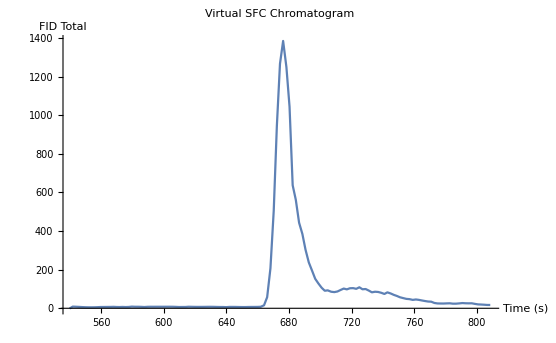

```mathematica
ListLinePlot[Partition[Riffle[d1,(Total[#]&/@data2d)[[All,3]]],2], PlotLabel->"Virtual SFC Chromatogram", AxesLabel->{"Time (s)","FID Total"}, PlotRange->{All, All}]
```

Create graphics for export to the thesis or publication:

```mathematica
exportgraphic = Show[
	plot3d
	,PlotLabel -> Style["FAMEs: Canola oil", Large, Bold, Black]
	, AxesStyle -> {Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				, Directive[Black, Bold, 15]
				}
	,AxesLabel-> 
		{Style["SFC (s)", Large, Bold, Black]
		, Style[ "GC (s)",Large, Bold, Black]
		,Style[Rotate["Detector (V)", 90 Degree], Large, Bold, Black]
		}
	(*, ViewPoint->{10000,10000,10000} *)
	, ImageSize-> 1024
	, ViewPoint->vp
	
]
```

```mathematica
Export["C:\\Users\\fskdm\\My PhD\\Conferences\\Analitika 2018\\Poster\\images\\Canola.png",exportgraphic,Background->None, ViewPoint->vp]
```

C:\Users\fskdm\My PhD\Conferences\Analitika 2018\Poster\images\Canola.png

```mathematica
Show[
	plot3d
(*	,Graphics3D[{Red,Line[data2d]}] *)
     , PlotLabel -> "Mystery Oil"
	, PlotRange-> {All, All,{0,0.1}}
]
```

```mathematica
contourplot = ListContourPlot[Flatten[data2d,1], PlotRange->{All, All, {0,5}}, AxesLabel->{"SFC (s)", "GC (s)"}]
```

-Graphics-

```mathematica
Show[contourplot, PlotRange->{All, All}]
```

-Graphics-